```mathematica
αassume={Subscript[α, 12]>=0,Subscript[α, 13]>=0,Subscript[α, 23]>=0};
λassume=Subscript[λ, 1]<0&&Subscript[λ, 2]<0;
μassume=0<μ<∞;
θassume=0<=θ<=π/2;
a=1/2;
h=1/Sqrt[3];
Subscript[yp, 1]={0,h};
Subscript[yp, 2]={-a,-h/2};
Subscript[yp, 3]={a,-h/2};
Hv={{Subscript[λ, 1],0},{0,Subscript[λ, 2]}};
Gv=FullSimplify[Inverse[RotationMatrix[θ]].Hv.RotationMatrix[θ]];
eqns={
Gv.Subscript[yp, 1]==Subscript[α, 12] (Subscript[yp, 2]-Subscript[yp, 1])+Subscript[α, 13] (Subscript[yp, 3]-Subscript[yp, 1]),
Gv.Subscript[yp, 2]==Subscript[α, 12] (Subscript[yp, 1]-Subscript[yp, 2])+Subscript[α, 23] (Subscript[yp, 3]-Subscript[yp, 2]),
Gv.Subscript[yp, 3]==Subscript[α, 13] (Subscript[yp, 1]-Subscript[yp, 3])+Subscript[α, 23] (Subscript[yp, 2]-Subscript[yp, 3])
};
αsolns=FullSimplify[Solve[eqns,{Subscript[α, 12],Subscript[α, 13],Subscript[α, 23]}]];
αμsolns=FullSimplify[αsolns/.{Subscript[λ, 1]->-Abs[Subscript[λ, 1]],Subscript[λ, 2]->-Abs[Subscript[λ, 2]]}/.{Abs[Subscript[λ, 2]]->μ Abs[Subscript[λ, 1]]},Subscript[λ, 1]<0];
μineq=αassume/.αμsolns;

ϕ[μ_]:=ArcCos[(μ+1)/(2 Abs[μ-1])]
θcond1[μ_]:=0<=θ<=π/6-ϕ[μ]/2||π/6+ϕ[μ]/2<=θ<=π/2-ϕ[μ]/2 (* 0 < μ < 1/3 *)
θcond2[μ_]:=0<=θ<=π/2 (* 1/3 <= μ <= 3 *)
θcond3[μ_]:=ϕ[μ]/2<=θ<=π/3-ϕ[μ]/2||π/3+ϕ[μ]/2<=θ<=π/2 (* 3 < μ < ∞ *)
θconds[μ_]:=Piecewise[{{θcond1[μ],0<μ<1/3},{θcond2[μ],1/3<=μ<=3},{θcond3[μ],3<μ}}] (* 0 < μ < ∞ *)
Gv//TraditionalForm
```

(λ_2 sin^2(θ)+λ_1 cos^2(θ) | (λ_2-λ_1) sin(θ) cos(θ)
(λ_2-λ_1) sin(θ) cos(θ) | λ_1 sin^2(θ)+λ_2 cos^2(θ))

```mathematica
MatrixForm[Flatten[First/@eqns]]==MatrixForm[Flatten[Last/@eqns]]//TraditionalForm
Column[First[αsolns]]⇒Column[First[αμsolns]]//TraditionalForm
Transpose[μineq]⇒Transpose[Simplify[μineq,λassume]]//TraditionalForm
θconds[μ]//TraditionalForm
```

(((λ_2-λ_1) sin(θ) cos(θ))/(√3)
(λ_1 sin^2(θ)+λ_2 cos^2(θ))/(√3)
1/2 (-λ_2 sin^2(θ)-λ_1 cos^2(θ))-((λ_2-λ_1) sin(θ) cos(θ))/(2 √3)
-(λ_1 sin^2(θ)+λ_2 cos^2(θ))/(2 √3)-1/2 (λ_2-λ_1) sin(θ) cos(θ)
1/2 (λ_2 sin^2(θ)+λ_1 cos^2(θ))-((λ_2-λ_1) sin(θ) cos(θ))/(2 √3)
1/2 (λ_2-λ_1) sin(θ) cos(θ)-(λ_1 sin^2(θ)+λ_2 cos^2(θ))/(2 √3))==(α_13/2-α_12/2
-1/2 √3 α_12-(√3 α_13)/2
α_12/2+α_23
(√3 α_12)/2
-α_13/2-α_23
(√3 α_13)/2)

α_12→1/3 ((√3 cos(θ)-sin(θ)) sin(θ) λ_1-cos(θ) (cos(θ)+√3 sin(θ)) λ_2)
α_13→1/3 (cos(θ) (√3 sin(θ)-cos(θ)) λ_2-sin(θ) (√3 cos(θ)+sin(θ)) λ_1)
α_23→1/6 ((2 cos(2 θ)-1) λ_2-(2 cos(2 θ)+1) λ_1)⇒α_12→1/3 Abs[λ_1] (μ cos^2(θ)+√3 (μ-1) sin(θ) cos(θ)+sin^2(θ))
α_13→1/3 Abs[λ_1] (μ cos^2(θ)-√3 (μ-1) sin(θ) cos(θ)+sin^2(θ))
α_23→1/6 Abs[λ_1] (μ-2 (μ-1) cos(2 θ)+1)

(1/3 Abs[λ_1] (μ cos^2(θ)+√3 (μ-1) sin(θ) cos(θ)+sin^2(θ))≥0
1/3 Abs[λ_1] (μ cos^2(θ)-√3 (μ-1) sin(θ) cos(θ)+sin^2(θ))≥0
1/6 Abs[λ_1] (-2 (μ-1) cos(2 θ)+μ+1)≥0)⇒(μ cos^2(θ)+√3 (μ-1) sin(θ) cos(θ)+sin^2(θ)≥0
μ cos^2(θ)+sin^2(θ)≥√3 (μ-1) sin(θ) cos(θ)
μ+1≥2 (μ-1) cos(2 θ))

Piecewise[{{0≤θ≤π/6-1/2 cos^-1((μ+1)/(2 Abs[μ-1]))∨1/2 cos^-1((μ+1)/(2 Abs[μ-1]))+π/6≤θ≤π/2-1/2 cos^-1((μ+1)/(2 Abs[μ-1])), 0<μ<1/3}, {0≤θ≤π/2, 1/3≤μ≤3}, {1/2 cos^-1((μ+1)/(2 Abs[μ-1]))≤θ≤π/3-1/2 cos^-1((μ+1)/(2 Abs[μ-1]))∨1/2 cos^-1((μ+1)/(2 Abs[μ-1]))+π/3≤θ≤π/2, 3<μ}}]

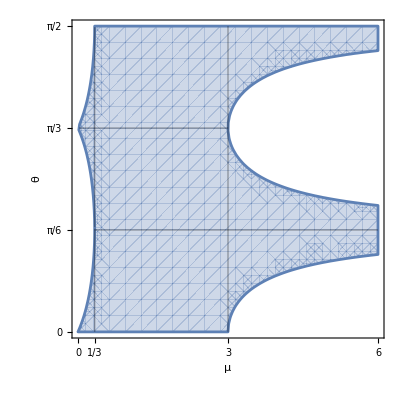

```mathematica
RegionPlot[θconds[μ],{μ,0,6},{θ,0,π/2},
FrameLabel->{"μ","θ"},RotateLabel->False,(*PlotLabel->"(μ,θ)-Feasibility Plot",*)FrameTicks->{{{{0,"0"},{π/6,"π/6"},{π/3,"π/3"},{π/2,"π/2"}},Automatic},{{{0,"0"},{1/3,"1/3"},{3,"3"},{6,"6"}},Automatic}},
PerformanceGoal->"Quality",
Mesh->{{1/3,3},{π/6,π/3}}
]
```

```mathematica
d1a[μ_]:=Disk[{0,0},1,{0,π/6-ϕ[μ]/2}]
d1b[μ_]:=Disk[{0,0},1,{π/6+ϕ[μ]/2,π/2-ϕ[μ]/2}]
d1[μ_]:=RegionUnion[d1a[μ],d1b[μ]]
d2[μ_]:=Disk[{0,0},1,{0,π/2}]
d3a[μ_]:=Disk[{0,0},1,{ϕ[μ]/2,π/3-ϕ[μ]/2}]
d3b[μ_]:=Disk[{0,0},1,{π/3+ϕ[μ]/2,π/2}]
d3[μ_]:=RegionUnion[d3a[μ],d3b[μ]]
d[μ_]:=Piecewise[{{d1[μ],0<μ<1/3},{d2[μ],1/3<=μ<=3},{d3[μ],3<μ}}]
```

```mathematica
Manipulate[Region[d[μ]],{μ,0.0001,6}]
```

Region::reg: d[6.] is not a correctly specified region.